# NR package

## by Ian Hinder

## Initialisation

```mathematica
<<"NR.m"
```

## Documentation

The NR package contains functions for dealing with NR waveforms, BH trajectories, apparent horizons, run statistics, convergence testing and more.

## Notes

This package is currently much too large and needs to be split up into subpackages.  For this reason, it is not documented fully here, only examples are given.

## NR Examples

```mathematica
run="D6q1_1a";
```

### ReadPsi4[runName, lMode, mMode, radius]

```mathematica
psi4=ReadPsi4[run,2,2,100]
```

DataTable[...]

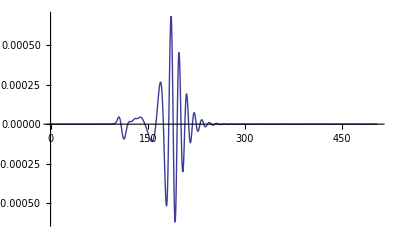

```mathematica
ListLinePlot[Re[psi4],PlotRange->All]
```

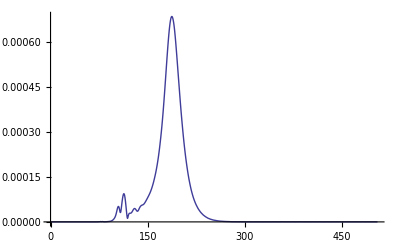

```mathematica
ListLinePlot[Abs[psi4],PlotRange->All]
```

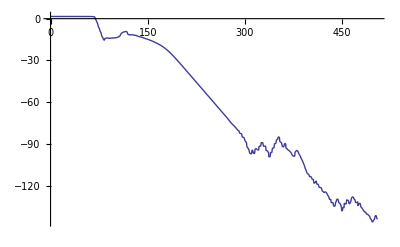

```mathematica
ListLinePlot[Phase[psi4],PlotRange->All]
```

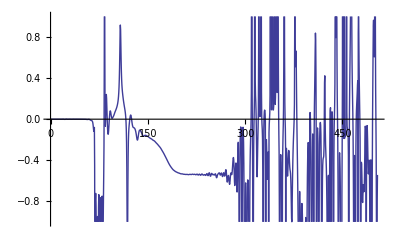

```mathematica
ListLinePlot[Frequency[psi4],PlotRange->{-1,1}]
```

### BH Trajectories

```mathematica
traj0=ReadBHTrajectory[run,0];
```

```mathematica
Take[traj0,10]
```

{{3,0},{2.99977,0.00514429},{2.99835,0.034876},{2.99577,0.0824581},{2.99226,0.138325},{2.98801,0.196708},{2.98306,0.254795},{2.97752,0.312379},{2.97142,0.369961},{2.96461,0.427684}}

```mathematica
traj1=ReadBHTrajectory[run,1];
```

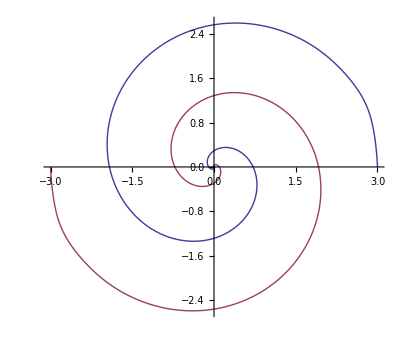

```mathematica
ListLinePlot[{traj0,traj1},PlotRange->All,AspectRatio->Automatic]
```

Separation of the BHs (radius of relative orbit)

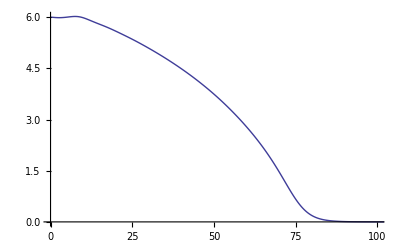

```mathematica
ListLinePlot[ReadBHSeparation[run],PlotRange->{{0,100},All}]
```

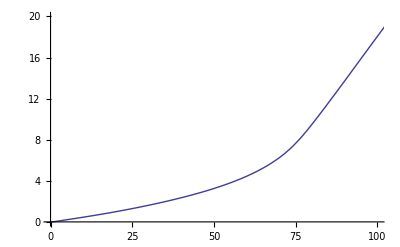

```mathematica
ListLinePlot[ReadBHPhase[run],PlotRange->{{0,100},{0,20}}]
```

### Individual coordinates

```mathematica
bh0x=ReadBHCoordinate[run,0,1]
```

DataTable[...]

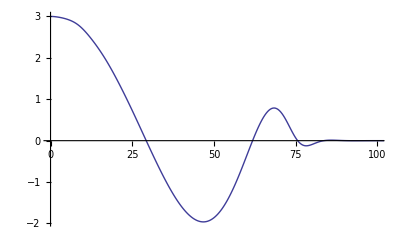

```mathematica
ListLinePlot[bh0x,PlotRange->{{0,100},All}]
```

### Apparent horizons

Remember that AHFinderDirect numbers its horizons from 1, not 0

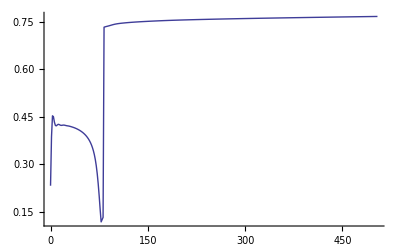

```mathematica
ListLinePlot[ReadAHRadius[run,1],PlotRange->{{0,100},{0,All}}]
```

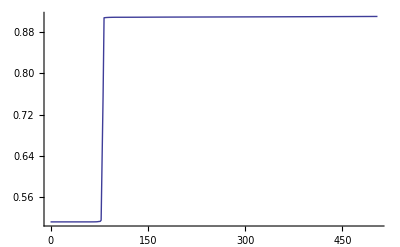

```mathematica
ListLinePlot[ReadAHMass[run,1],PlotRange->{{0,100},{0,All}}]
```

### Isolated horizons

IsolatedHorizon numbers horizons from 0

```mathematica
spin=ReadIsolatedHorizonSpin[run,0]
```

DataTable[...]

```mathematica
Take[ToList[spin],10]
```

{{0,{1.42951×10^-16,7.47864×10^-18,1.18493×10^-8}},{1.5,{3.2936×10^-16,-6.53291×10^-17,-9.06758×10^-6}},{3,{1.34051×10^-16,-9.65427×10^-17,5.29152×10^-6}},{4.5,{2.99366×10^-16,-1.07675×10^-16,-0.0000217553}},{6,{5.15519×10^-16,1.61102×10^-17,-0.000059066}},{7.5,{7.23715×10^-16,1.09618×10^-16,-0.0000612243}},{9,{3.32497×10^-15,1.32581×10^-15,0.0000300866}},{10.5,{1.32572×10^-14,1.02207×10^-14,0.000157086}},{12,{-4.30332×10^-14,-3.81644×10^-14,0.000155773}},{13.5,{-5.82457×10^-14,-5.38381×10^-15,0.0000671962}}}

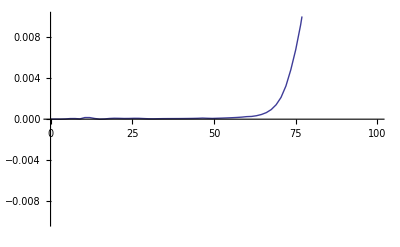

```mathematica
ListLinePlot[Norm[spin],PlotRange->{{0,100},{-0.01,0.01}}]
```